# Tools

## Basic Headers—make sure that the “dataDir” is correctly linked

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/rigers/Documents/GitHub/ML-correlator/Graph_Edge_Data

```mathematica
fourPointDataDir="../consolidated_data";
```

```mathematica
niceTime[timeInSec_]:=If[timeInSec<($TimeUnit/100)||Not[NumericQ[timeInSec]]||Precision[timeInSec]==0,"",Block[{measure=Select[Transpose[{(Quotient[Mod[timeInSec,#1],#2]&@@@Partition[{timeInSec 10,3.15569277216*^7,3600*24.,3600.,60.,1.,10^-3,10.^-6,10.^-9},2,1]),{" years"," days"," hours"," minutes"," seconds"," ms"," μs"," ns"}}],#[[1]]>0&]},If[Length[measure]>0,Row[Row[#,""]&/@measure[[1;;Min[2,Length[measure]]]],", "],""]]];
map[function_,list_]:=If[Length[list]>0,Module[{monitor=0,len=Length[list],newFcn,t00=AbsoluteTime[]},newFcn[i_]:=(monitor=i;function[list[[i]]]);Monitor[Map[newFcn,Range[len]],(Column[{ProgressIndicator[(monitor-1)/len,ImageSize->{1250,30},ImageMargins->0,BaselinePosition->Center],If[monitor≥1,Row[{If[monitor>1,Row[{niceTime[Round[AbsoluteTime[]-t00]]," so far; approx. ",niceTime[Round[((AbsoluteTime[]-t00)/(monitor-1))*(len-monitor+1)]]," remaining."}],"                                              "]," (",monitor-1,"/",len,")"}],""]},Alignment->Left,Spacings->0.1])]],Map[function,list]];
littleGroup[graph_]:=Block[{num=Numerator[graph],den=Denominator[graph]},num=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[num][[2;;-1]]);den=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[den][[2;;-1]]);-(Count[num,#,{0,∞}]-Count[den,#,{0,∞}])&/@Sort[DeleteDuplicates[Flatten[List@@@Cases[graph,_x,{0,∞}]]]]];
```

## Basic Data Analysis (same as before)

```mathematica
planarGraphDials[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_dials_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[planarGraphDials[loop],ReadList[fileName]],{{}}]];
planarGraphEdges[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_edges_"<>ToString[loop]<>".tex"))}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];Set[planarGraphEdges[loop],(raw/.rule)]),{{}}]];
fGraphNums[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];raw=Times@@@#&/@(x@@@#&/@#&/@(raw/.rule));Set[fGraphNums[loop],raw]),{{}}]];
fGraphList[loop_]:=If[FileExistsQ[FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}]],Set[fGraphList[loop],(Join@@(fGraphNums[loop](1/(Times@@@(x@@@#&/@planarGraphEdges[loop])))))],{{}}];

amplitudeCoefficients[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("amplitudeCoefficients_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[amplitudeCoefficients[loop],(<<(fileName))],{}]];
```

## Graph Analysis (with a few new face-extraction tools)

```mathematica
graphIsomorphisms[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,((bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])),(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])])]];
graphIsomorphism[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,Thread[Rule[baseLabels,baseLabels]],(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&,1])])])]];
graphEquivalentQ[fcnList__]/;(Length[{fcnList}]==2):=Not[graphIsomorphism[fcnList]==={}];
distinctGraphs[seedList_]:=DeleteDuplicates[seedList,graphEquivalentQ];
graphAutomorphisms[graph_]:=graphIsomorphisms[graph,graph];
graphSymmetryFactor[graph_]:=Length[graphAutomorphisms[graph]];
canonicalizeGraph[graph_]:=Block[{baseEdges=List@@@DeleteDuplicates[Cases[Denominator[graph],x[y__],{0,∞}]],baseLabels,baseGraph,auto},baseLabels=DeleteDuplicates[Flatten[baseEdges]];baseGraph=Graph[UndirectedEdge@@@baseEdges];auto=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@FindGraphIsomorphism[baseGraph,CanonicalGraph[baseGraph]])[[1]];graph/.{x[q__]:>x@@(Sort[{q}/.auto])}];

orderedVertsToFaces[dialList_]:=Block[{edgeRules,fullEdgeList},edgeRules=Join@@Table[(Rule[{#1,j},{j,#2}]&@@@Partition[dialList[[j]],2,1,1]),{j,Length[dialList]}];fullEdgeList=edgeRules[[All,1]];Sort@DeleteDuplicates[Function[{start},(Function[{term},Sort[Partition[Reverse@term,Length[term],1,1]][[1]]]@DeleteDuplicates[Join@@NestWhile[Append[#,(#[[-1]]/.edgeRules)]&,{start},Length[DeleteDuplicates[#]]==Length[#]&]])]/@fullEdgeList]];
externalTuples[faceList_]:=Block[{triples=Select[faceList,Length[#]==3&],quads=Select[faceList,Length[#]==4&]},Function[{face},Sort[Join[Partition[face,4,1,1],Partition[Reverse@face,4,1,1]]][[1]]]/@Join[quads,Function[{x,y},DeleteDuplicates[Join@@{RotateLeft[x,Flatten[Position[x,Complement[x,y][[1]]]][[1]]+1],RotateLeft[y,Flatten[Position[y,Complement[y,x][[1]]]][[1]]]}]]@@@(Select[Subsets[triples,{2}],Length[DeleteDuplicates[Join@@#]]==4&])]];
externalFaces[nPt_:3,0][faceList_]:=Which[nPt≤2,{{}},nPt===3,Select[faceList,Length[#]==nPt&],True,Block[{newFaces=Select[faceList,Length[#]==nPt&]},DeleteDuplicates[Join[newFaces,(Join@@Table[(Function[{pair},Block[{edges=Partition[#,2,1,1]&/@pair},Sort[Partition[#,Length[#],1,1]][[1]]&@DeleteDuplicates[Join@@(edges[[1]]/.(Function[{list},Reverse[list[[1]]]->(Sequence@@list[[2;;-1]])]/@Partition[edges[[2]],Length[edges[[2]]],1,1]))]]]/@Select[DeleteDuplicates[Sort/@DeleteCases[Tuples[{externalFaces[nPt-jJ,0][faceList],externalFaces[jJ+2,0][faceList]}],{x_,x_}]],Length[Intersection@@#]==2&]),{jJ,1,Floor[(nPt-2)/2]}])]]]];
externalFaces[nPt_:4,1][faceList_]:=Block[{ptList=Sort[DeleteDuplicates[Flatten[faceList]]]},DeleteCases[Function[{ptNo},Block[{adjList=Select[faceList,MemberQ[#,ptNo]&]},If[(Total[(Length[#]-2)&/@adjList]==nPt)&&(Length[adjList]==nPt),(Function[{ring},Block[{edgeList=Select[Partition[#,Length[#]-1,1,1],Not[MemberQ[#,ptNo]]&][[1]]&/@ring,edgeRules},{ptNo,(Sort[Partition[#,Length[#],1,1]][[1]]&@DeleteDuplicates[Nest[Function[{pChain},Join[pChain,Select[edgeList,#[[1]]===pChain[[-1]]&,1][[1]]]],edgeList[[1]],Length[edgeList]-1]])}]]@adjList),{}]]]/@ptList,{}]];
specialPents[faceList_]:=Block[{squares,triangles,seeds},triangles=Select[faceList,Length[#]==3&];squares=Select[faceList,Length[#]==4&];seeds=Function[{shared,pair},{shared,(Join@@(Function[{q},Select[Partition[q,Length[q],1,1],#[[1]]==shared&,1][[1,2;;-1]]]/@pair))}]@@@({(Intersection@@#)[[1]],#}&/@Select[Tuples[{squares,triangles}],Length[Intersection@@#]==1&]);{#1,RotateLeft[#2]}&@@@Select[seeds,Function[{anchor,pent},Block[{missing},missing=Function[{face},Sort[Partition[face,Length[face],1,1]][[1]]]/@((Prepend[#,anchor]&/@{pent[[{3,4}]],pent[[{5,1}]]}));Length[Intersection[missing,triangles]]==2]]@@#&]];
```

## Some Interesting Extensions (relative to what I sent before)

```mathematica
drawGraph[dials_,extFace_:{},labelsQ_:False]:=Block[{distinctFaces,faceList=orderedVertsToFaces[dials],edgeList=Sort[DeleteDuplicates[Join@@(Function[{y,z},Sort[{y,#}]&/@z]@@@(Transpose[{Range[Length[dials]],dials}]))]],valencies,face,autos},valencies=Count[edgeList,#,{0,∞}]&/@Sort[DeleteDuplicates[Flatten[edgeList]]];faceList=faceList[[Ordering[{Length[#],-Variance[valencies[[#]]]}&/@faceList]]];autos=graphAutomorphisms[Power[Times@@x@@@edgeList,-1]];distinctFaces=Gather[faceList,SameQ[Sort[Sort/@(#1/.autos)][[1]],Sort[Sort/@(#2/.autos)][[1]]]&][[All,1]];face=Which[extFace==={},(distinctFaces[[-1]]),Head[extFace]===Integer,distinctFaces[[-Mod[extFace,Length[distinctFaces],1]]],True,extFace];face=Join[Partition[face,Length[face],1,1],Partition[Reverse@face,Length[face],1,1]];face=face[[Ordering[valencies/@#&/@face][[-1]]]];Block[{vList=v/@Sort[DeleteDuplicates[Flatten[edgeList]]],bdyLen=Length[face],spiderWeight=2.25,vRules,spiderMetric,soln,intVs=Complement[Sort[DeleteDuplicates[Flatten[edgeList]]],face],thickness=1,pointsize=7.5,imageSize=200,out},vRules=Join[Thread[Rule[v/@(face),({Cos[2π/bdyLen*(#-1)],Sin[2π/bdyLen*(#-1)]}&/@Range[bdyLen])]],Thread[Rule[v/@intVs,{x[#],y[#]}&/@intVs]]];spiderMetric=Total/@Power[((#1-#2&@@@(v/@#&/@edgeList))/.vRules),2];spiderMetric=Total[Power[spiderMetric,spiderWeight/2]];vRules=(vRules/.NMinimize[( spiderMetric),Variables[vRules[[All,2]]],AccuracyGoal->5][[2]]);out=Graphics[Join[{CapForm["Round"],AbsoluteThickness[thickness],Line[#/.vRules]}&/@(v/@#&/@edgeList),{AbsolutePointSize[pointsize],Point[#]}&/@vRules[[All,2]],If[TrueQ[labelsQ],({Text[#[[1]],{0.05,0.05}+(#/.vRules)]}&/@vList),{}]],ImageSize->imageSize,PlotRange->{{-1.1,1.1},{-1.1,1.1}}];(*Function[{img},(First@ImportString[ExportString[img,"PDF"],"PDF","TextMode"->"Outlines"])]@out*)out]];
conformalDressings[edgeList_]:=Module[
{vList=Sort[DeleteDuplicates[Flatten[edgeList]]],
numList,autos,weights,eph,excluded},
weights=DeleteCases[({#,Count[Flatten[edgeList],#]-4}&/@Sort[DeleteDuplicates[Flatten[edgeList]]]),{x_,0}];
numList=Which[Length[weights]==0,
	{{}},
	Length[weights]==1,
	{},Length[weights]==2,
	If[And[SameQ@@weights[[All,2]],
		Not[MemberQ[edgeList,weights[[All,1]]]]],
		{(weights[[1;;2,1]]&/@Range[weights[[1,2]]])},{}],
	True,
	(excluded=Intersection[Subsets[weights[[All,1]],{2}],edgeList];
eph=FixedPoint[Join@@(Function[{num,remaining},Which[remaining==={},{{num,remaining}},Length[remaining]==1,{},True,Block[{ordering=remaining[[All,1]],next=Complement[({remaining[[1,1]],#}&/@remaining[[2;;-1,1]]),excluded]},
If[Length[next]==0,{},({Append[num,#],DeleteCases[ReplacePart[remaining,{{1,2}->(remaining[[1,2]]-1),{(#[[2]]/.Thread[Rule[ordering,Range[Length[remaining]]]]),2}->(remaining[[((#[[2]]/.Thread[Rule[ordering,Range[Length[remaining]]]])),2]]-1)}],{x_,0}]}&/@next)]]]]@@@#)&,{{{},weights}}];
If[eph==={},{},(DeleteDuplicates[Sort/@eph[[All,1]]])])];Which[numList==={},{},numList==={{}},{1},True,(autos=graphAutomorphisms[Power[(Times@@(x@@@edgeList)),-1]];If[Length[autos]==1,Times@@@(x@@@#&/@numList),(Times@@@(x@@@#&/@Sort[DeleteDuplicates[(Sort[#][[1]]&/@(Sort/@#&/@(Sort/@#&/@#&/@(Transpose[numList/.autos]))))]]))])]];
```

# Extraction

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/gabriele/Documents/GitHub/ML-correlator/Graph_Edge_Data

### Functions

```mathematica
SetAttributes[ProdToList,Listable]
ProdToList[x_]:=Block[{Times=List,Power=Table},If[Head[x]===List,Flatten@x,{x}]]
```

```mathematica
ExpToDenominatorGraph[x_List]:=ExpToDenominatorGraph[#]&/@x
ExpToDenominatorGraph[x_List,v_]:=ExpToDenominatorGraph[#,v]&/@x
ExpToDenominatorGraph[t_]:=Graph[UndirectedEdge@@@ProdToList@Denominator[t],VertexLabels->"Name"]
ExpToDenominatorGraph[t_,vert_List]:=Module[{temp},
temp=Denominator[t];
If[temp===1,Graph[vert,{}],
Graph[vert,UndirectedEdge@@@ProdToList@temp,VertexLabels->"Name"]]
]
```

```mathematica
ExpToNumeratorGraph[x_List]:=ExpToDenominatorGraph[#]&/@x
ExpToNumeratorGraph[x_List,v_]:=ExpToDenominatorGraph[#,v]&/@x
ExpToNumeratorGraph[t_]:=If[Numerator[t]===1,Graph[VertexList@ExpToDenominatorGraph[t],{}],Graph[VertexList@ExpToDenominatorGraph[t],UndirectedEdge@@@ProdToList@Numerator[t]]]
ExpToNumeratorGraph[t_,vert_List]:=Module[{temp},
temp=Denominator[t];
If[temp===1,Graph[vert,{}],
Graph[vert,UndirectedEdge@@@ProdToList@temp,VertexLabels->"Name"]]
]
```

```mathematica
Clear[denGraph]
denGraph[l_]:=denGraph[l]=ExpToDenominatorGraph/@fGraphList[l]
```

```mathematica
Clear[numGraph]
numGraph[l_]:=numGraph[l]=ExpToNumeratorGraph/@fGraphList[l]
```

```mathematica
(*Gives the edges of a graph as String in the notation of the phyton library networkx, that is a list of tuples*)
edgeListNX[graph_Graph]:=
StringReplace[StringReplace[ StringReplace[ToString[EdgeList[graph]/. UndirectedEdge->List],{"{"->"(","}"->")"}],{"(("->"[(","))"->")]"}],"()"->"[]"]
edgeListNX[graph_List]:=StringReplace[StringReplace[ StringReplace[ToString[graph/. UndirectedEdge->List],{"{"->"(","}"->")"}],{"(("->"[(","))"->")]"}],"()"->"[]"]
```

```mathematica
graphDataCSV[l_]:=Module[{data,csv},
data =Transpose[{amplitudeCoefficients[l],edgeListNX/@denGraph[l],edgeListNX/@numGraph[l]}];
csv=Prepend[data,{"COEFFICIENTS","DEN_EDGES","NUM_EDGES"}];
Export["graph_data_"<>ToString[l]<>".csv",csv]
]
```

```mathematica
denCoefficients[l_]:= Module[{multNum},
multNum=Length/@fGraphNums[l];
Boole/@(Or@@@TakeList[#!=0&/@amplitudeCoefficients[l],multNum])
]
```

```mathematica
denGraphDataCSV[l_]:=Module[{data,csv},
data =Transpose[{denCoefficients[l],edgeListNX/@planarGraphEdges[l]}];
csv=Prepend[data,{"COEFFICIENTS","EDGES"}];
Export["den_graph_data_"<>ToString[l]<>".csv",csv]
]
```

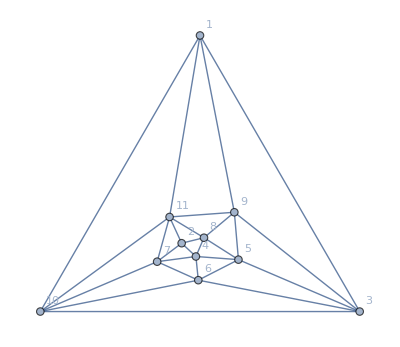

```mathematica
PlanarGraph@ExpToDenominatorGraph@fGraphList[7][[1]]
```

```mathematica
AdjacencyMatrix[%]
```

SparseArray[…]

```mathematica
%//Normal
```

{{0,1,1,1,1,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,1,1},{1,1,0,0,1,0,0,0,1,1,0},{1,1,0,0,1,0,0,1,0,0,1},{1,0,1,1,0,1,0,1,1,0,0},{0,0,0,0,1,0,1,1,1,0,0},{0,0,0,0,0,1,0,1,1,1,1},{0,0,0,1,1,1,1,0,0,0,1},{0,0,1,0,1,1,1,0,0,1,0},{0,1,1,0,0,0,1,0,1,0,1},{0,1,0,1,0,0,1,1,0,1,0}}

```mathematica
StringReplace[%,{
```

## Save csv with edges

```mathematica
graphDataCSV[9]
```

graph_data_9.csv

```mathematica
denGraphDataCSV[10]
```

$Aborted

## Building csv eigenvalues

```mathematica
l=10;
```

```mathematica
fGraphList[l];
```

### coefficients

```mathematica
column ={"COEFFICIENT_DEN"}
coef = Transpose[{Boole[#!=0]&/@amplitudeCoefficients[l]}];
csv1=Prepend[coef,column];
```

{COEFFICIENT_DEN}

### Spectrum

```mathematica
<<"allEigenF.wl";
```

We take the spectrum of the denominator graph and the spectrum of the f-graph marking with negative sign the dashed edges

```mathematica
allEigenD=ParallelMap[approx[#,6]&/@Sort[Eigenvalues[N[AdjacencyMatrix[Graph[#]]]]]&,denGraph[l]];
```

```mathematica
allEigenF =ParallelMap[Sort[Eigenvalues[N[AdjacencyMatrix[ExpToDenominatorGraph[#]]-AdjacencyMatrix[ExpToNumeratorGraph[#]]]]]&,fGraphList[l]];
```

```mathematica
"DEN_EIGEN"<>ToString[#]&/@ Range[l+4];
"FGRAPH_EIGEN"<>ToString[#]&/@ Range[l+4];
column =Join[%%,%]
```

{DEN_EIGEN1,DEN_EIGEN2,DEN_EIGEN3,DEN_EIGEN4,DEN_EIGEN5,DEN_EIGEN6,DEN_EIGEN7,DEN_EIGEN8,DEN_EIGEN9,DEN_EIGEN10,DEN_EIGEN11,DEN_EIGEN12,DEN_EIGEN13,DEN_EIGEN14,FGRAPH_EIGEN1,FGRAPH_EIGEN2,FGRAPH_EIGEN3,FGRAPH_EIGEN4,FGRAPH_EIGEN5,FGRAPH_EIGEN6,FGRAPH_EIGEN7,FGRAPH_EIGEN8,FGRAPH_EIGEN9,FGRAPH_EIGEN10,FGRAPH_EIGEN11,FGRAPH_EIGEN12,FGRAPH_EIGEN13,FGRAPH_EIGEN14}

```mathematica
data =Transpose[Join[Transpose[allEigenD],Transpose[allEigenF]]];
csv2=Prepend[data,column];
```

```mathematica
csv2[[2]]//Length
```

28

### Join csv

```mathematica
csv=Transpose[Join@@(Transpose/@{csv1,csv2})];
```

```mathematica
Export["fgraph_eigen_10.csv",csv]
```

fgraph_eigen_10.csv

```mathematica
csv//Dimensions
```

{900146,29}

```mathematica
Take[csv,5]//TableForm
```

COEFFICIENT_DEN | DEN_EIGEN1 | DEN_EIGEN2 | DEN_EIGEN3 | DEN_EIGEN4 | DEN_EIGEN5 | DEN_EIGEN6 | DEN_EIGEN7 | DEN_EIGEN8 | DEN_EIGEN9 | DEN_EIGEN10 | DEN_EIGEN11 | DEN_EIGEN12 | DEN_EIGEN13 | DEN_EIGEN14 | FGRAPH_EIGEN1 | FGRAPH_EIGEN2 | FGRAPH_EIGEN3 | FGRAPH_EIGEN4 | FGRAPH_EIGEN5 | FGRAPH_EIGEN6 | FGRAPH_EIGEN7 | FGRAPH_EIGEN8 | FGRAPH_EIGEN9 | FGRAPH_EIGEN10 | FGRAPH_EIGEN11 | FGRAPH_EIGEN12 | FGRAPH_EIGEN13 | FGRAPH_EIGEN14
0 | -2.36147 | -2.30893 | -2. | -2. | -1.81295 | -1.06984 | -1. | -0.414214 | -0.167449 | 0.119329 | 2.41421 | 2.52892 | 2.88697 | 5.18543 | -3.69624 | -2.79756 | -2.73733 | -2.44086 | -1.6726 | -1.48959 | -0.62055 | 0.140528 | 0.450277 | 0.784405 | 2.57527 | 3.62463 | 3.87961 | 4.
0 | -2.36147 | -2.30893 | -2. | -2. | -1.81295 | -1.06984 | -1. | -0.414214 | -0.167449 | 0.119329 | 2.41421 | 2.52892 | 2.88697 | 5.18543 | -3.62992 | -2.84684 | -2.69372 | -2.3005 | -1.78413 | -1.46922 | -0.811272 | 0.199064 | 0.396535 | 0.747539 | 2.71501 | 3.52914 | 3.9483 | 4.
0 | -2.36147 | -2.30893 | -2. | -2. | -1.81295 | -1.06984 | -1. | -0.414214 | -0.167449 | 0.119329 | 2.41421 | 2.52892 | 2.88697 | 5.18543 | -3.66896 | -3.07037 | -2.71833 | -2.67068 | -1.69643 | -1.29895 | -0.448706 | 0.381614 | 0.708129 | 0.870774 | 2.18519 | 3.53357 | 3.89316 | 4.
0 | -2.36147 | -2.30893 | -2. | -2. | -1.81295 | -1.06984 | -1. | -0.414214 | -0.167449 | 0.119329 | 2.41421 | 2.52892 | 2.88697 | 5.18543 | -3.44094 | -2.96793 | -2.63979 | -2.13045 | -1.64335 | -1.4009 | -0.714477 | -0.301851 | 0.420685 | 0.863772 | 2.76452 | 3.31213 | 3.87858 | 4.

### find identical rows position

```mathematica
data =Transpose[Join[Transpose[allEigenD],Transpose[approx[#,6]&/@allEigenF]]];
```

```mathematica
dul6=Select[GatherBy[Range[Length[data]],data[[#]]&],Length[#]>1&];
```

```mathematica
dul6[[1]]
```

{4041,4315}

```mathematica
Flatten[coef[[#]]]&/@dul6;
%//DeleteDuplicates
```

{{0,0},{1,0},{1,1},{0,1},{0,0,0},{0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Flatten[dul6]//Length
```

3308

```mathematica
Flatten[coef[[#]]]&/@dul6;
Position[%,#,1]&/@{{1,0},{0,1}}
res =Extract[dul6,#]&/@%
```

{{{2},{24},{89}},{{23}}}

{{{4657,4725},{290978,290995},{672011,672029}},{{280496,281030}}}

Missmatch

```mathematica
[4724,7075,19810,281029,290977,291224,291226,672010,824379]
```

```mathematica
Position[res,#]&/@({4724,7075,19810,281029,290977,291224,291226,672010,824379}+1)
Flatten[Extract[res,#]&/@%]
```

{{{1,1,2}},{},{},{{2,1,2}},{{1,2,1}},{},{},{{1,3,1}},{}}

{4725,281030,290978,672011}

```mathematica
{{{4657,4725},{290978,290995},{672011,672029}},{{280496,281030}}}-1
```

{{{4656,4724},{290977,290994},{672010,672028}},{{280495,281029}}}

## Building csv eigenvalues Only Denominator

```mathematica
l=10;
```

### coefficients

```mathematica
column ={"COEFFICIENT_DEN"}
data = Transpose[{denCoefficients[l]}];
csv1=Prepend[data,column];
```

{COEFFICIENT_DEN}

```mathematica
denCoefficients[l]//Length
```

153252

### Spectrum

We take the spectrum of the denominator graph and the spectrum of the f-graph marking with negative sign the dashed edges

```mathematica
allEigenD=ParallelMap[Sort[Eigenvalues[N[AdjacencyMatrix[Graph[#]]]]]&,(Graph/@planarGraphEdges[l])];
```

```mathematica
"DEN_EIGEN"<>ToString[#]&/@ Range[l+4];
column =%
```

{DEN_EIGEN1,DEN_EIGEN2,DEN_EIGEN3,DEN_EIGEN4,DEN_EIGEN5,DEN_EIGEN6,DEN_EIGEN7,DEN_EIGEN8,DEN_EIGEN9,DEN_EIGEN10,DEN_EIGEN11,DEN_EIGEN12,DEN_EIGEN13,DEN_EIGEN14}

```mathematica
data =allEigenD;
csv2=Prepend[data,column];
```

```mathematica
Take[csv2,5]//TableForm
```

DEN_EIGEN1 | DEN_EIGEN2 | DEN_EIGEN3 | DEN_EIGEN4 | DEN_EIGEN5 | DEN_EIGEN6 | DEN_EIGEN7 | DEN_EIGEN8 | DEN_EIGEN9 | DEN_EIGEN10 | DEN_EIGEN11 | DEN_EIGEN12 | DEN_EIGEN13 | DEN_EIGEN14
-2.36147 | -2.30893 | -2. | -2. | -1.81295 | -1.06984 | -1. | -0.414214 | -0.167449 | 0.119329 | 2.41421 | 2.52892 | 2.88697 | 5.18543
-2.49163 | -2. | -2. | -2. | -2. | -1.11233 | -0.732051 | -0.554352 | -1.21541×10^-15 | 0.0826453 | 2.20749 | 2.73205 | 2.83563 | 5.03254
-2.36147 | -2.31489 | -2. | -2. | -1.77264 | -1.06244 | -1. | -0.353747 | -0.167449 | 0.248641 | 2.37135 | 2.52892 | 2.82752 | 5.0562
-2.58388 | -2.18371 | -2. | -2. | -1.72055 | -1.07821 | -0.685097 | -0.245004 | -0.214215 | 0.167653 | 2.20713 | 2.53884 | 2.87023 | 4.9268

```mathematica
csv2//Length
```

153253

### Join csv

```mathematica
csv=Transpose[Join@@(Transpose/@{csv1,csv2})];
```

```mathematica
Export["den_eigen_10.csv",csv]
```

den_eigen_10.csv

```mathematica
csv//Dimensions
```

{153253,15}

```mathematica
Take[csv,5]//TableForm
```

COEFFICIENT_DEN | DEN_EIGEN1 | DEN_EIGEN2 | DEN_EIGEN3 | DEN_EIGEN4 | DEN_EIGEN5 | DEN_EIGEN6 | DEN_EIGEN7 | DEN_EIGEN8 | DEN_EIGEN9 | DEN_EIGEN10 | DEN_EIGEN11 | DEN_EIGEN12
1 | -2.47283 | -2.15671 | -2. | -1.4626 | -1.31948 | -1. | -0.715172 | -0.414214 | 1.93543 | 2.13996 | 2.41421 | 5.0514
1 | -2.44258 | -2.23607 | -2. | -1.32557 | -1. | -1. | -1. | -0.414214 | 1.90542 | 2.23607 | 2.41421 | 4.86272
1 | -2.23607 | -2.23607 | -2.23607 | -1. | -1. | -1. | -1. | -1. | 2.23607 | 2.23607 | 2.23607 | 5.
1 | -2.47511 | -2.10684 | -2. | -1.64179 | -1.53209 | -0.979173 | -0.347296 | -0.244395 | 1.81165 | 1.87939 | 2.53578 | 5.09989

### find identical rows position

```mathematica
dulDEi=Select[GatherBy[Range[Length[allEigenD]],allEigenD[[#]]&],Length[#]>1&];
```

$Aborted

```mathematica
allEigenD6=f[allEigenD,6];
```

```mathematica
dul6=Select[GatherBy[Range[Length[allEigenD6]],allEigenD6[[#]]&],Length[#]>1&];
```

```mathematica
Flatten[data[[#]]]&/@dul6;
Position[%,{0,1},1]
Position[%%,{1,0},1]
```

{{6},{10},{12},{52},{53},{95},{117},{319},{320}}

{{7},{9},{24},{91},{123}}

```mathematica
[217,789,795,799,825,4002,4159,4162,4965,4998,5674,6165,6204,6218,6228,6242,11644,20307,20542,20674,21414,23585,23731,24050,24052,24056,24094,24573,24581,25117,26064,26231,26233,26265,26827,26828,26833,26837,28491,28640,29690,30110,31600,32340,32341,33027,33172,33177,33557,34415,34442,34995,35026,36815,38230,38442,38649,38650,38651,38984,39042,39156,41696,42874,42890,43065,43504,43511,43831,44628,46600,46695,46698,46982,47509,47620,47681,47828,47846,48201,49935,49938,50248,50265,51703,52138,52829,52832,52847,52912,53175,53305,53310,53467,53660,54394,55233,57153,58133,58830,60154,61014,62946,62954,62974,63001,63006,63142,63145,63179,63219,63227,63436,67072,67077,68503,68532,69728,70003,70018,70020,70037,71209,78166,78168,78170,78886,79777,79782,79849,80466,80487,81096,81994,83398,84792,84793,84862,84863,84977,85770,85781,86554,86561,86564,86570,86587,86597,86602,94941,96338,96524,103504,103542,103992,104118,105751,105761,105900,105917,106047,106050,106141,107168,107498,108472,108483,109054,109351,112528,112998,113184,113900,114053,118388,118428,118710,120401,120915,122492,122935,126641,135542,138973]
```

```mathematica
Flatten[dul6]//Length
```

2186

```mathematica
dul6[[1]]
```

{29923,149843}

```mathematica
allEigenD6[[#]]&/@dul6;
First/@%;
Rationalize[Take[%,5],0.01]
```

{{-53/21,-26/11,-2,-20/11,-14/9,-30/31,-6/11,-1/8,2/7,11/14,8/7,5/3,11/3,13/3},{-17/7,-20/9,-2,-2,-13/8,-5/8,-11/23,-2/7,0,5/8,4/3,13/8,26/7,35/8},{-19/8,-23/10,-2,-2,-11/7,-6/5,-7/15,0,3/8,1/2,19/20,19/10,26/7,85/19},{-31/11,-5/2,-19/10,-13/8,-8/5,-9/11,-6/13,-1/9,1/6,5/8,6/7,26/15,34/9,14/3},{-8/3,-34/15,-23/11,-13/8,-8/5,-29/28,-9/19,-1/16,2/7,5/8,3/4,23/12,41/11,9/2}}

```mathematica
Flatten[Flatten[data[[#]]]&/@dul6]//DeleteDuplicates
```

{0}

## Building csv Kirchhoff Only Denominator

```mathematica
l=10;
```

### coefficients

```mathematica
column ={"COEFFICIENT_DEN"}
data = Transpose[{denCoefficients[l]}];
csv1=Prepend[data,column];
```

{COEFFICIENT_DEN}

```mathematica
denCoefficients[l]//Length
```

153252

### Spectrum

We take the spectrum of the denominator graph and the spectrum of the f-graph marking with negative sign the dashed edges

```mathematica
allEigenD=ParallelMap[Sort[Eigenvalues[N[KirchhoffMatrix[Graph[#]]]]]&,(Graph/@planarGraphEdges[l])];
```

```mathematica
"DEN_EIGEN"<>ToString[#]&/@ Range[l+4];
column =%
```

{DEN_EIGEN1,DEN_EIGEN2,DEN_EIGEN3,DEN_EIGEN4,DEN_EIGEN5,DEN_EIGEN6,DEN_EIGEN7,DEN_EIGEN8,DEN_EIGEN9,DEN_EIGEN10,DEN_EIGEN11,DEN_EIGEN12,DEN_EIGEN13,DEN_EIGEN14}

{DEN_EIGEN1,DEN_EIGEN2,DEN_EIGEN3,DEN_EIGEN4,DEN_EIGEN5,DEN_EIGEN6,DEN_EIGEN7,DEN_EIGEN8,DEN_EIGEN9,DEN_EIGEN10,DEN_EIGEN11,DEN_EIGEN12,DEN_EIGEN13,DEN_EIGEN14}

```mathematica
data =allEigenD;
csv2=Prepend[data,column];
```

```mathematica
Take[csv2,5]//TableForm
```

DEN_EIGEN1 | DEN_EIGEN2 | DEN_EIGEN3 | DEN_EIGEN4 | DEN_EIGEN5 | DEN_EIGEN6 | DEN_EIGEN7 | DEN_EIGEN8 | DEN_EIGEN9 | DEN_EIGEN10 | DEN_EIGEN11 | DEN_EIGEN12 | DEN_EIGEN13 | DEN_EIGEN14
-2.36147 | -2.30893 | -2. | -2. | -1.81295 | -1.06984 | -1. | -0.414214 | -0.167449 | 0.119329 | 2.41421 | 2.52892 | 2.88697 | 5.18543
-2.49163 | -2. | -2. | -2. | -2. | -1.11233 | -0.732051 | -0.554352 | -1.21541×10^-15 | 0.0826453 | 2.20749 | 2.73205 | 2.83563 | 5.03254
-2.36147 | -2.31489 | -2. | -2. | -1.77264 | -1.06244 | -1. | -0.353747 | -0.167449 | 0.248641 | 2.37135 | 2.52892 | 2.82752 | 5.0562
-2.58388 | -2.18371 | -2. | -2. | -1.72055 | -1.07821 | -0.685097 | -0.245004 | -0.214215 | 0.167653 | 2.20713 | 2.53884 | 2.87023 | 4.9268

```mathematica
csv2//Length
```

153253

### Join csv

```mathematica
csv=Transpose[Join@@(Transpose/@{csv1,csv2})];
```

```mathematica
Export["den_Kirchhoff_10.csv",csv]
```

den_Kirchhoff_10.csv

```mathematica
csv//Dimensions
```

{153253,15}

```mathematica
Take[csv,5]//TableForm
```

COEFFICIENT_DEN | DEN_EIGEN1 | DEN_EIGEN2 | DEN_EIGEN3 | DEN_EIGEN4 | DEN_EIGEN5 | DEN_EIGEN6 | DEN_EIGEN7 | DEN_EIGEN8 | DEN_EIGEN9 | DEN_EIGEN10 | DEN_EIGEN11 | DEN_EIGEN12 | DEN_EIGEN13 | DEN_EIGEN14
1 | -9.32832×10^-16 | 1.98064 | 2.60523 | 2.93576 | 4.60001 | 5.23562 | 5.46477 | 6.19633 | 6.24424 | 7. | 7. | 7. | 7.77457 | 7.96282
1 | -1.36654×10^-16 | 1.98064 | 2.26795 | 2.93576 | 4.60001 | 5. | 5.46477 | 5.73205 | 6.24424 | 7. | 7. | 7. | 7. | 7.77457
1 | -1.45794×10^-15 | 1.89366 | 2.5959 | 2.66703 | 4.5105 | 4.7006 | 5.285 | 6.15644 | 6.21846 | 6.6754 | 7. | 7. | 7.47593 | 7.82108
1 | 3.23852×10^-16 | 1.87585 | 2.22275 | 2.66636 | 4.45288 | 4.66504 | 5. | 5.63016 | 6.20812 | 6.56565 | 7. | 7. | 7. | 7.71317

```mathematica
Take[csv1,100]
```

{{COEFFICIENT_DEN},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{0},{1},{1},{1},{0},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{0},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{0},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
VertexConnectivity[planarGraphEdges[l][[3]]]
```

4

### find identical rows position

0.1666

```mathematica
dulDEi=Select[GatherBy[Range[Length[allEigenD]],allEigenD[[#]]&],Length[#]>1&];
```

$Aborted

```mathematica
N[allEigenD6[[1,1]],1]
```

-9.32832×10^-16

```mathematica
allEigenD6=f[#,10]&/@allEigenD;
```

```mathematica
dul6=Select[GatherBy[Range[Length[allEigenD6]],allEigenD6[[#]]&],Length[#]>1&];
```

```mathematica
Flatten[data[[#]]]&/@dul6
```

{{1,1},{0,1},{1,1},{1,1},{0,0},{0,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{1,1},{0,0},{0,0,0},{0,0},{0,0},{1,1},{1,1},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,1},{1,1},{1,1},{0,0},{1,1},{1,1},{1,1},{0,1},{0,0},{1,1},{0,1},{0,1},{0,0},{1,0},{1,1},{0,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,1},{0,0},{1,1},{1,1},{1,1},{1,1},{0,0},{1,1},{1,1},{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{0,0},{1,0},{1,1},{1,1},{0,0},{1,0},{1,1},{1,0},{1,0},{1,1},{1,0},{1,0},{0,0},{0,1},{1,0},{1,1},{0,0},{0,0},{0,0},{1,1},{1,1},{0,0},{1,1},{0,1},{0,0},{0,0},{1,1},{1,1},{0,0},{0,0},{1,1},{0,0},{0,0},{1,1},{1,1},{0,0},{0,0},{1,1},{0,0},{0,0},{1,1},{1,1},{0,0},{1,1},{0,0},{1,1},{0,0},{0,0},{1,1},{0,1},{1,0},{0,0},{1,1},{0,0},{1,1},{1,1},{0,0},{0,0},{0,0},{0,1},{0,0},{0,0},{1,1},{1,1},{1,1},{0,0},{1,1},{0,0},{1,1},{1,0},{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1},{0,0},{1,0},{0,0},{1,0},{0,1},{0,0},{0,0},{1,1},{0,1},{1,1},{0,0},{0,1},{0,0},{1,1},{1,0},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1},{1,1},{1,1},{0,1},{1,1},{1,1},{0,1},{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1},{0,0},{1,1},{0,0},{1,1},{1,1},{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{0,0},{0,0},{1,1},{0,0},{1,1},{1,1},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,1},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,0},{0,0},{0,1},{0,1},{1,1},{1,1},{1,0},{1,1},{1,1},{0,0},{0,1},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,1},{0,1},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,1},{1,1},{0,0},{0,0},{1,1},{0,0},{0,0},{0,1},{1,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{1,0},{1,0},{1,0},{0,0},{0,0},{1,1},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,1},{0,0},{1,0},{0,0},{0,0},{0,1},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{1,1},{1,1,1},{0,0},{0,0},{1,1},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{1,1},{0,1,0,1},{1,1},{0,1},{0,0},{1,1},{0,0},{0,0},{0,0},{0,1},{0,0},{0,0},{0,1,1},{0,0},{0,1},{0,0},{1,1},{1,0},{0,0},{1,1},{0,0},{0,1},{1,0},{1,1},{0,0},{1,1},{0,0},{0,0},{0,0},{0,1},{1,1},{1,1},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{0,1},{0,1},{0,0},{0,0},{1,1},{0,1},{1,1},{1,1},{1,1},{1,1},{1,1},{0,1},{1,0},{1,1},{1,1},{0,0},{1,1},{1,1},{1,1},{1,1},{1,1},{0,0},{0,1},{1,1},{1,1},{1,0},{1,0},{1,1},{0,1},{1,1},{1,1},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{1,1},{1,1},{0,0},{0,0},{0,0},{0,1},{0,0},{1,1},{0,0},{1,1},{1,1},{0,0},{1,1},{1,1},{0,1},{0,1},{0,0},{1,1},{0,0},{1,1},{1,1},{1,1},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{1,1},{1,1},{0,0},{1,1},{1,1},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{1,1},{1,1},{1,1},{0,0},{0,1,1},{0,0},{1,1,1},{1,1},{1,0,0},{0,1,0},{0,1},{0,0,0},{1,1,1},{0,1},{1,1},{1,0,1},{0,1,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{1,1},{1,1},{0,0},{0,0},{0,1},{0,0},{0,0},{0,0},{1,1},{1,0,1},{1,1},{1,1},{0,0},{1,0},{1,1},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{1,1},{1,1},{0,0},{1,1},{1,1},{0,0},{0,1},{0,1},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{1,1},{0,0},{1,1},{1,1},{1,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{1,1},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{0,1},{0,0},{0,1},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{1,1},{0,0},{1,1},{0,0},{1,1},{0,0},{0,1},{1,1},{0,0},{0,1},{0,1},{0,1},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,1},{0,0},{1,1,1},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,1},{0,0},{0,0},{1,1},{0,0},{1,1},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{1,1},{1,1},{0,0},{1,1},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,1},{1,1},{1,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0,0,0,0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0,0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0,0,0,0,0},{0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0,0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{0,1},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0,0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0,0,0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
Flatten[dul6]//Length
```

2186

```mathematica
dul6[[1]]
```

{29923,149843}

```mathematica
allEigenD6[[#]]&/@dul6;
First/@%;
Rationalize[Take[%,5],0.01]
```

{{-53/21,-26/11,-2,-20/11,-14/9,-30/31,-6/11,-1/8,2/7,11/14,8/7,5/3,11/3,13/3},{-17/7,-20/9,-2,-2,-13/8,-5/8,-11/23,-2/7,0,5/8,4/3,13/8,26/7,35/8},{-19/8,-23/10,-2,-2,-11/7,-6/5,-7/15,0,3/8,1/2,19/20,19/10,26/7,85/19},{-31/11,-5/2,-19/10,-13/8,-8/5,-9/11,-6/13,-1/9,1/6,5/8,6/7,26/15,34/9,14/3},{-8/3,-34/15,-23/11,-13/8,-8/5,-29/28,-9/19,-1/16,2/7,5/8,3/4,23/12,41/11,9/2}}

```mathematica
Flatten[Flatten[data[[#]]]&/@dul6]//DeleteDuplicates
```

{0}

## Building csv only den

```mathematica
l=10;
```

### Coefficient ignoring numerator

```mathematica
multNum=Length/@fGraphNums[l];
amplitudeCoefficients[l];
Boole/@(Or@@@TakeList[#!=0&/@%,%%]);
N[Count[%,0]/Length[%]] 100
```

66.5499

```mathematica
multNum=Length/@fGraphNums[l];
amplitudeCoefficients[l];
TakeList[#!=0&/@%,%%];
Or@@@%;
coefDen =Boole/@Flatten[Table@@@Thread[{%,multNum}]];
```

```mathematica
column ={"COEFFICIENT_DEN"}
data = Transpose[{coefDen}];
csv1=Prepend[data,column];
```

{COEFFICIENT_DEN}

### Random Walk from adjacency matrix traces

```mathematica
Clear[adjMatPower]
adjMatPower[graph_,k_]:= adjMatPower[graph,k-1].AdjacencyMatrix[graph]
adjMatPower[graph_,1]:= adjMatPower[graph,1] =AdjacencyMatrix[graph]
```

```mathematica
numOfkWalks [graph_,k_]:=1/2 Tr@adjMatPower[graph,k]
```

```mathematica
maxWalkLen = l+4;
```

```mathematica
myfgraph[l_] := Thread[f[numGraph[l],denGraph[l]]]/.f->GraphUnion;
```

```mathematica
denWalks =Table[numOfkWalks[#,i]&/@denGraph[l],{i,2,maxWalkLen}];
fgraphWalks =Table[numOfkWalks[#,i]&/@myfgraph[l],{i,2,maxWalkLen}];
```

```mathematica
"DEN_WALKS"<>ToString[#]&/@ Range[2,maxWalkLen];
"FGRAPH_WALKS"<>ToString[#]&/@ Range[2,maxWalkLen];
column =Join[%%,%]
```

{DEN_WALKS2,DEN_WALKS3,DEN_WALKS4,DEN_WALKS5,DEN_WALKS6,DEN_WALKS7,DEN_WALKS8,DEN_WALKS9,DEN_WALKS10,DEN_WALKS11,DEN_WALKS12,FGRAPH_WALKS2,FGRAPH_WALKS3,FGRAPH_WALKS4,FGRAPH_WALKS5,FGRAPH_WALKS6,FGRAPH_WALKS7,FGRAPH_WALKS8,FGRAPH_WALKS9,FGRAPH_WALKS10,FGRAPH_WALKS11,FGRAPH_WALKS12}

```mathematica
data = Transpose[Join[denWalks,fgraphWalks]];
csv2=Prepend[data,column];
```

```mathematica
Take[csv2,-10]//TableForm
```

24 | 36 | 224 | 640 | 2784 | 9856 | 39424 | 149760 | 589824 | 2297856 | 9058304 | 24 | 36 | 224 | 640 | 2784 | 9856 | 39424 | 149760 | 589824 | 2297856 | 9058304
25 | 36 | 245 | 705 | 3340 | 12215 | 52665 | 209682 | 882350 | 3624115 | 15172802 | 26 | 39 | 290 | 885 | 4577 | 17787 | 83034 | 351840 | 1591161 | 6959282 | 31160477
26 | 42 | 282 | 880 | 4259 | 16569 | 74086 | 310767 | 1363966 | 5876937 | 25711383 | 28 | 54 | 376 | 1400 | 7360 | 33138 | 164192 | 780912 | 3818448 | 18463016 | 90020032
27 | 42 | 327 | 1020 | 5409 | 21378 | 101759 | 439242 | 2024747 | 9037864 | 41291949 | 30 | 66 | 486 | 2010 | 11220 | 54936 | 290766 | 1492770 | 7823250 | 40717446 | 213104196
27 | 42 | 327 | 1020 | 5409 | 21378 | 101759 | 439242 | 2024747 | 9037864 | 41291949 | 30 | 60 | 478 | 1930 | 11064 | 53942 | 288494 | 1480992 | 7793630 | 40582366 | 212740780
27 | 48 | 351 | 1140 | 5865 | 23310 | 108927 | 467796 | 2129727 | 9441300 | 42767757 | 30 | 66 | 486 | 2010 | 11220 | 54936 | 290766 | 1492770 | 7823250 | 40717446 | 213104196
28 | 54 | 392 | 1380 | 7324 | 31192 | 153184 | 699624 | 3366768 | 15810256 | 75730352 | 31 | 78 | 559 | 2580 | 14713 | 77770 | 429583 | 2341698 | 12889191 | 70788036 | 389656717
26 | 48 | 326 | 1060 | 5132 | 19908 | 88270 | 364728 | 1580906 | 6703180 | 28951700 | 28 | 60 | 408 | 1560 | 8032 | 36176 | 176928 | 838752 | 4075648 | 19674688 | 95752320
26 | 48 | 326 | 1060 | 5132 | 19908 | 88270 | 364728 | 1580906 | 6703180 | 28951700 | 28 | 60 | 408 | 1560 | 8032 | 36176 | 176928 | 838752 | 4075648 | 19674688 | 95752320
30 | 66 | 486 | 2010 | 11220 | 54936 | 290766 | 1492770 | 7823250 | 40717446 | 213104196 | 33 | 102 | 729 | 3930 | 23853 | 140742 | 843729 | 5047410 | 30265173 | 181481982 | 1088667129

### Number of facets

```mathematica
fGraphListcycles=orderedVertsToFaces/@planarGraphDials[l];
```

```mathematica
maxLenght =Max[Length/@Flatten[fGraphListcycles,1]]
```

6

```mathematica
numberOfFaces[faces_List,maxLenght_]:= Count[Length/@faces,#]&/@Range[3,maxLenght]
```

```mathematica
faceMult=numberOfFaces[#,maxLenght]&/@fGraphListcycles;
```

```mathematica
column ="FACES_MULT"<>ToString[#]&/@ Range[3,maxLenght]
```

{FACES_MULT3,FACES_MULT4,FACES_MULT5,FACES_MULT6}

```mathematica
data = faceMult;
csv3=Prepend[data,column];
```

```mathematica
Take[csv3,-10]//TableForm
```

13 | 2 | 1 | 0
12 | 0 | 0 | 2
12 | 1 | 2 | 0
14 | 0 | 2 | 0
14 | 3 | 0 | 0
14 | 3 | 0 | 0
16 | 2 | 0 | 0
14 | 1 | 0 | 1
14 | 0 | 2 | 0
20 | 0 | 0 | 0

### Number of Cycles

set max cycle to the number of facets

```mathematica
maxCycleLength=maxLenght
```

6

```mathematica
(* Find all cycles *)
findAllCyclesMult[graph_]:= FindCycle[graph,VertexCount[graph],maxCycleLength]
```

```mathematica
allCycles = ParallelMap[findAllCyclesMult,denGraph[l]];
```

```mathematica
numberOfCycles[cycles_List,maxLenght_]:= Count[Length/@cycles,#]&/@Range[3,maxLenght]
```

```mathematica
cyclesMult =ParallelMap[numberOfCycles[#,maxCycleLength]&,allCycles];
```

```mathematica
column ="CYCLES_MULT"<>ToString[#]&/@ Range[3,maxCycleLength]
```

{CYCLES_MULT3,CYCLES_MULT4,CYCLES_MULT5,CYCLES_MULT6}

```mathematica
data = cyclesMult;
csv4=Prepend[data,column];
```

```mathematica
Take[csv,3]//TableForm
```

CYCLES_MULT3 | CYCLES_MULT4 | CYCLES_MULT5 | CYCLES_MULT6 | CYCLES_MULT7 | CYCLES_MULT8 | CYCLES_MULT9 | CYCLES_MULT10 | CYCLES_MULT11
18 | 29 | 78 | 234 | 566 | 1018 | 1322 | 1152 | 508
18 | 29 | 78 | 234 | 566 | 1018 | 1322 | 1152 | 508

### Number of double triangles

```mathematica
allTriangles = FindCycle[#,3,All]&/@denGraph[l];
```

```mathematica
doubleTriangleNumber[triangles_]:=Total[Length/@ (Intersection@@@Subsets[triangles,{2}])]
```

```mathematica
dtNumber =doubleTriangleNumber/@allTriangles;
```

```mathematica
column ={"DOUBLE_TRIANGLES"}
```

{DOUBLE_TRIANGLES}

```mathematica
data = Transpose[{dtNumber}];
csv5=Prepend[data,column];
```

```mathematica
Take[csv5,-6]//TableForm
```

5
12
17
14
14
26

### Connectivity

```mathematica
connectivity = VertexConnectivity/@denGraph[l];
```

```mathematica
column ={"CONNECTIVITY"}
```

{CONNECTIVITY}

```mathematica
data = Transpose[{connectivity}];
csv6=Prepend[data,column];
```

```mathematica
Take[csv6,-5]//TableForm
```

3
2
2
2
3

### Join csv

```mathematica
csv=Transpose[Join@@(Transpose/@{csv1,csv2,csv3,csv4,csv5,csv6})];
```

Transpose::nmtx: The first two levels of {{COEFFICIENT_DEN,1,1,1,1,1,1,1,1,1,«2700»},{DEN_WALKS2,30,30,30,30,30,30,30,30,30,«2700»},{DEN_WALKS3,60,60,60,60,60,60,60,60,60,«2700»},«6»,{DEN_WALKS10,5419310,5419310,5419310,5419310,5419310,5419310,5419310,5419310,5419310,«2700»},«23»} cannot be transposed.

```mathematica
Join@@(Transpose/@{csv1,csv2,csv3,csv4,csv5,csv6});
%[[-7]]
```

{FACES_MULT6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,1,0,0}